```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/richardbrower/Desktop/GitHUB_QuantumGeometry/mathematica

```mathematica
Clear[AffineTable]
```

```mathematica
(* AffineTable := Import["CutUniform48.dat"]*)
```

```mathematica
AffineTable := 
Import["../data/CutUniform48.dat"]
```

```mathematica
data := AffineTable[[All, {1,2}]]
```

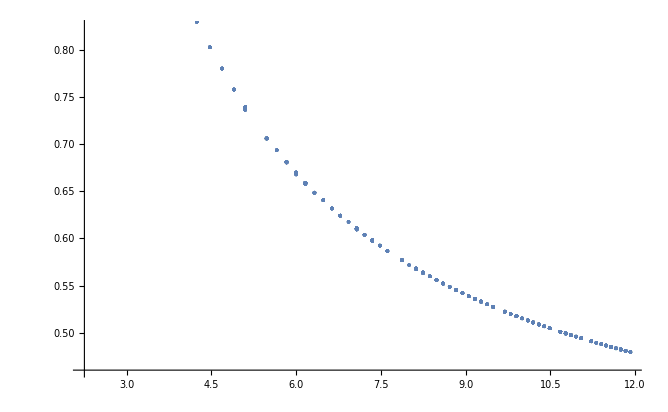

```mathematica
ListPlot[data]
```

```mathematica
(* nlmYuk=NonlinearModelFit[data,a Exp[ - b x]/x^c +d ,{a,b,c,d},x,Method->"QuasiNewton"]*)
nlmCoul=NonlinearModelFit[data,a /x^c +d ,{a,c,d},x,Method->"QuasiNewton"]
(*Method->"Newton" *)
```

FittedModel[0.298403+2.42592/x^1.04848]

```mathematica
Normal[nlmCoul]
```

0.298403+2.42592/x^1.04848

```mathematica
nlmCoul[{"BestFit","ParameterTable"}]
```

{0.298403+2.42592/x^1.04848, | Estimate | Standard Error | t-Statistic | P-Value
a | 2.42592 | 0.00108093 | 2244.28 | 0.
c | 1.04848 | 0.00055272 | 1896.94 | 0.
d | 0.298403 | 0.000192692 | 1548.6 | 0.}

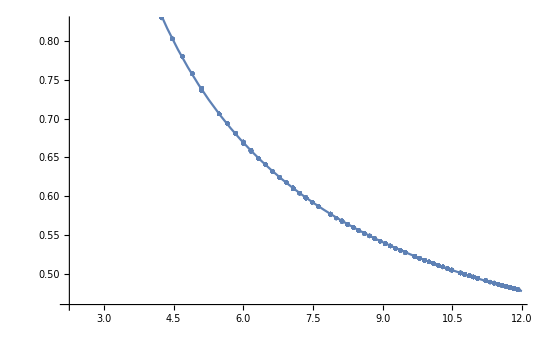

```mathematica
Show[ListPlot[data,PlotStyle->PointSize[Medium]], Plot[nlmCoul[x], {x, 1, 12}]]
```

```mathematica
nlmYuk["FitResiduals"];
nlmYuk["Properties"]
```

nlmYuk[Properties]

```mathematica
dataxyz= AffineTable[[All, {3,4,5,2}]];
```

```mathematica
r[x_,y_,z_,gyy_,gzz_, gxy_, gyz_, gzx_]:= Sqrt[x^2 + gyy  y^2 + gzz z^2 + gxy x*y   + gyz y *z  + gzx z* x];
```

```mathematica
nlmAffine=NonlinearModelFit[dataxyz, a /r[x,y,z, gyy,gzz, gxy, gyz, gzx]^c +d ,{a,c,d, {gyy,1}, {gzz,1}, { gxy,.1}, {gyz, .1}, {gzx, .1} },{x,y,z},Method->"LevenbergMarquardt"]
```

FittedModel[0.297988+2.41517/((«8»+1. z^2)^0.523616)]

```mathematica
Normal[nlmAffine]
```

0.297988+2.41517/((x^2-0.0103573 x y+1. y^2-0.0103573 x z-0.0103573 y z+1. z^2)^0.523616)

```mathematica
nlmAffine[{"BestFit","ParameterTable"}]
```

{0.297988+2.41517/((x^2-0.0103573 x y+1. y^2-0.0103573 x z-0.0103573 y z+1. z^2)^0.523616), | Estimate | Standard Error | t-Statistic | P-Value
a | 2.41517 | 0.00116482 | 2073.42 | 0.
c | 1.04723 | 0.000514412 | 2035.78 | 0.
d | 0.297988 | 0.000179697 | 1658.28 | 0.
gyy | 1. | 0.000575083 | 1738.88 | 0.
gzz | 1. | 0.000575083 | 1738.88 | 0.
gxy | -0.0103573 | 0.000863042 | -12.0009 | 1.49739×10^-32
gyz | -0.0103573 | 0.000866351 | -11.9551 | 2.54719×10^-32
gzx | -0.0103573 | 0.000863042 | -12.0009 | 1.49739×10^-32}

```mathematica
nlmAffineYuk=NonlinearModelFit[dataxyz, a Exp[ - b r[x,y,z,gyy,gzz, gxy, gyz, gzx]]/r[x,y,z,gyy,gzz, gxy, gyz, gzx]^c +d ,{{a,2},{b,0}, {c,1},{d,.3}, {gyy,1}, {gzz,1}, { gxy,.1}, {gyz, .1}, {gzx, .1} },{x,y,z},Method->"LevenbergMarquardt"]
```

FittedModel[0.353424+(2.40167 ⅇ^(-«20» «1»))/(«8»+«19» «1»)^0.502014]

```mathematica
Normal[nlmAffineYuk]
```

0.353424+(2.40167 ⅇ^(-0.0390565 √(x^2-0.0112236 x y+1. y^2-0.0112236 x z-0.0112236 y z+1. z^2)))/((x^2-0.0112236 x y+1. y^2-0.0112236 x z-0.0112236 y z+1. z^2)^0.502014)

```mathematica
nlmAffineYuk[{"BestFit","ParameterTable"}]
```

{0.353424+(2.40167 ⅇ^(-0.0390565 √(x^2-0.0112236 x y+1. y^2-0.0112236 x z-0.0112236 y z+1. z^2)))/((x^2-0.0112236 x y+1. y^2-0.0112236 x z-0.0112236 y z+1. z^2)^0.502014), | Estimate | Standard Error | t-Statistic | P-Value
a | 2.40167 | 0.00139966 | 1715.89 | 0.
b | 0.0390565 | 0.00108304 | 36.0619 | 9.67024×10^-243
c | 1.00403 | 0.00191508 | 524.275 | 0.
d | 0.353424 | 0.00110594 | 319.57 | 0.
gyy | 1. | 0.000540096 | 1851.52 | 0.
gzz | 1. | 0.000540096 | 1851.52 | 0.
gxy | -0.0112236 | 0.000811109 | -13.8373 | 1.90879×10^-42
gyz | -0.0112236 | 0.000814473 | -13.7802 | 4.05176×10^-42
gzx | -0.0112236 | 0.000811109 | -13.8373 | 1.90879×10^-42}

```mathematica
rsqr[x_,y_,z_] = x^2-0.011223572272895352 x y+1.0000000000000002 y^2-0.011223572272895155 x z-0.011223572272896123 y z+1.0000000000000002 z^2
```

x^2-0.0112236 x y+1. y^2-0.0112236 x z-0.0112236 y z+1. z^2

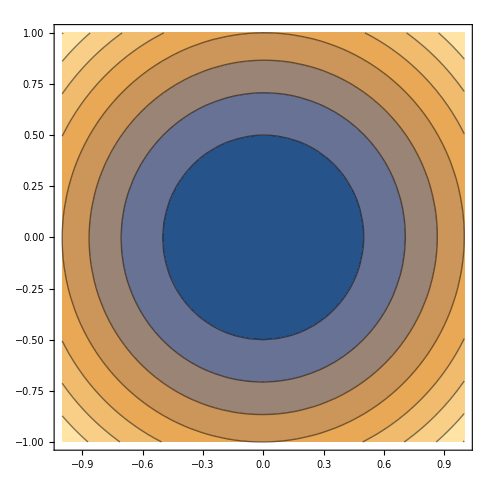

```mathematica
ContourPlot[rsqr[0,x,y],{x,-1,1},{y,-1,1}]
```

```mathematica
Plot3D[rsqr[x,y,0],{x,-1,1},{y,-1,1}]
```

-Graphics3D-